```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Wed 31 Jan 2018 15:19:48

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.1.0 (December 27, 2017)

## At Day 9

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

## 3 Areas, Integrals, and Accumulation

## Lab 19: Summation

### Introduction

```mathematica
SCAFE[∑_(i=1)^n 6,SCEvalSum]
```

∑_(i=1)^n 6==6 n

SCSumChangeInterval changes the interval of summation. The validity of equation is up to the user.

```mathematica
SCAFE[∑_(i=1)^n 6,SCSumChangeInterval,{All,{i,1,n-1}},$,Apply->SCEvalSum]
```

∑_(i=1)^n 6==6 ∑_(i=1)^(-1+n) 1

SCSumChangeLimits changes the interval of summation and keeps the validity of the equation.

```mathematica
SCAFE[∑_(i=1)^n 6,SCSumChangeLimits,{All,{i,1,n-1}},$,Apply->SCEvalSum]
```

∑_(i=1)^n 6==6+6 ∑_(i=1)^(-1+n) 1

Gauss’ sum trick

```mathematica
Grid@{Range[10],Reverse@Range[10],Range[10]+Reverse@Range[10]}
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
10 | 9 | 8 | 7 | 6 | 5 | 4 | 3 | 2 | 1
11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11 | 11

```mathematica
SCAFE[∑_(i=1)^n i,SCEvalSum]
```

∑_(i=1)^n i==1/2 n (1+n)

Exercises:

Derivation of an equation for the sum of squared natural numbers.

```mathematica
∑_(i=1)^n i^2==a n^3+b n^2+c n+d
SCMAF[%,Table[#/.n->l,{l,4}]&,All,Apply->SCEvalSum,
SCSolve,{All,{a,b,c,d}}]
```

∑_(i=1)^n i^2==d+c n+b n^2+a n^3

{1==a+b+c+d,5==8 a+4 b+2 c+d,14==27 a+9 b+3 c+d,30==64 a+16 b+4 c+d}

{a==1/3,b==1/2,c==1/6,d==0}

```mathematica
∑_(i=1)^n i^2==a n^3+b n^2+c n+d
SCMAF[%,RA,{At[2],{a==1/3,b==1/2,c==1/6,d==0}},Apply->Factor]
```

∑_(i=1)^n i^2==d+c n+b n^2+a n^3

∑_(i=1)^n i^2==1/6 n (1+n) (1+2 n)

```mathematica
SCAFE[∑_(i=1)^n i^2,SCEvalSum]
```

∑_(i=1)^n i^2==1/6 n (1+n) (1+2 n)

Derivation of an equation for the sum of cubed natural numbers.

```mathematica
∑_(i=1)^n i^3==a n^4+b n^3+c n^2+d n+e
SCMAF[%,Table[#/.n->l,{l,5}]&,All,Apply->SCEvalSum,
SCSolve,{All,{a,b,c,d,e}}]
```

∑_(i=1)^n i^3==e+d n+c n^2+b n^3+a n^4

{1==a+b+c+d+e,9==16 a+8 b+4 c+2 d+e,36==81 a+27 b+9 c+3 d+e,100==256 a+64 b+16 c+4 d+e,225==625 a+125 b+25 c+5 d+e}

{a==1/4,b==1/2,c==1/4,d==0,e==0}

```mathematica
∑_(i=1)^n i^3==a n^4+b n^3+c n^2+d n+e
SCMAF[%,RA,{At[2],{a==1/4,b==1/2,c==1/4,d==0,e==0}},Apply->Factor]
```

∑_(i=1)^n i^3==e+d n+c n^2+b n^3+a n^4

∑_(i=1)^n i^3==1/4 n^2 (1+n)^2

```mathematica
SCAFE[∑_(i=1)^n i^3,SCEvalSum]
```

∑_(i=1)^n i^3==1/4 n^2 (1+n)^2

## Lab 20: Riemann Sums

### Introduction

Exercises:

Demonstration: Riemann Sums

```mathematica
{Subscript[L, n]==∑_(i=0)^(n-1) (b-a)/n f[a+(i(b-a))/n],Subscript[R, n]==∑_(i=1)^n (b-a)/n f[a+(i(b-a))/n]}
SCMAF[%,RA,{All,f[x_]->x^2-1}]
```

{L_n==∑_(i=0)^(-1+n) (-a+b)/n f[a+((-a+b) i)/n],R_n==∑_(i=1)^n (-a+b)/n f[a+((-a+b) i)/n]}

{L_n==∑_(i=0)^(-1+n) (-a+b)/n (-1+(a+((-a+b) i)/n)^2),R_n==∑_(i=1)^n (-a+b)/n (-1+(a+((-a+b) i)/n)^2)}

```mathematica
Table[Subscript[L, n]==∑_(i=0)^(-1+n) (-a+b)/n (-1+(a+((-a+b) i)/n)^2),{n,{4,10,100}}]
SCMAF[%,RA,{All,{a==1,b==4}},
SCEvalSum,All,Apply->N]
```

{L_4==∑_(i=0)^3 1/4 (-a+b) (-1+(a+1/4 (-a+b) i)^2),L_10==∑_(i=0)^9 1/10 (-a+b) (-1+(a+1/10 (-a+b) i)^2),L_100==∑_(i=0)^99 1/100 (-a+b) (-1+(a+1/100 (-a+b) i)^2)}

{L_4==3/4 ∑_(i=0)^3 (-1+(1+(3 i)/4)^2),L_10==3/10 ∑_(i=0)^9 (-1+(1+(3 i)/10)^2),L_100==3/100 ∑_(i=0)^99 (-1+(1+(3 i)/100)^2)}

{L_4==12.6563,L_10==15.795,L_100==17.7755}

```mathematica
SCAFE[∫_1^4 (x^2-1)ⅆx,SCEvalInt,Apply->N]
```

∫_1^4 (-1+x^2)ⅆx==18.

Use infinitely many rectangles,

```mathematica
SCARA[Underscript[Limit, n->∞][Subscript[L, n]],Subscript[L, n]==∑_(i=0)^(-1+n) (-a+b)/n (-1+(a+((-a+b) i)/n)^2)]
SCMAF[%,SCEvalSum,At[2],Apply->{ExpandAll,SCEvalLimit}]
```

Limit_(n→∞)[L_n]==Limit_(n→∞)[∑_(i=0)^(-1+n) (-a+b)/n (-1+(a+((-a+b) i)/n)^2)]

Limit_(n→∞)[L_n]==a-a^3/3-b+b^3/3

```mathematica
SCARA[Underscript[Limit, n->∞][Subscript[R, n]],Subscript[R, n]==∑_(i=1)^n (-a+b)/n (-1+(a+((-a+b) i)/n)^2)]
SCMAF[%,SCEvalSum,At[2],Apply->{ExpandAll,SCEvalLimit}]
```

Limit_(n→∞)[R_n]==Limit_(n→∞)[∑_(i=1)^n (-a+b)/n (-1+(a+((-a+b) i)/n)^2)]

Limit_(n→∞)[R_n]==a-a^3/3-b+b^3/3

```mathematica
{Underscript[Limit, n->∞][Subscript[L, n]]==a-a^3/3-b+b^3/3,Underscript[Limit, n->∞][Subscript[R, n]]==a-a^3/3-b+b^3/3}/.{a->1,b->4}//N
```

{Limit_(n→∞)[L_n]==18.,Limit_(n→∞)[R_n]==18.}

lim_(n→∞) L_n=lim_(n→∞) R_n approaches the definite integral, ∫_a^b f[x]ⅆx.

```mathematica
∫_a^b f[x]ⅆx==Underscript[Limit, n->∞][∑_(i=0)^(n-1) (b-a)/n f[a+(i(b-a))/n]];
```

## Lab 21: The Definite and Indefinite Integral

### Definite Integrals

Exercises:

f[x]==-1+x

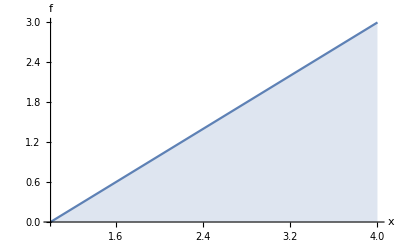

```mathematica
f[x]==x-1
SCMAF[%,Plot,{At[2],{x,1,4},AxesLabel->{x,f},{Filling->Axis}},Take->{2}]
```

```mathematica
SCAFE[∫_1^4 (x-1)ⅆx,SCEvalInt]
```

∫_1^4 (-1+x)ⅆx==9/2

f[x]==-1+x

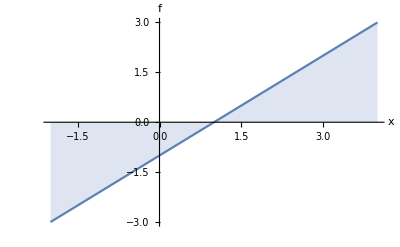

```mathematica
f[x]==x-1
SCMAF[%,Plot,{At[2],{x,-2,4},AxesLabel->{x,f},{Filling->Axis}},Take->{2}]
```

```mathematica
SCAFE[∫_-2^4 (x-1)ⅆx,SCEvalInt]
```

∫_-2^4 (-1+x)ⅆx==0

The area is

```mathematica
SCAFE[∫_-2^4 Abs[x-1]ⅆx,SCIntChangeInterval,{All,{x,{-2,1},{1,4}}}]
SCMAF[%,RA,{{∫_-2^1 |-1+x|ⅆx,Abs[f_]->-f},{∫_1^4 |-1+x|ⅆx,Abs[f_]->f}},Apply->SCEvalInt]
```

∫_-2^4 |-1+x|ⅆx==∫_-2^1 |-1+x|ⅆx+∫_1^4 |-1+x|ⅆx

∫_-2^4 |-1+x|ⅆx==9

f[x]==Sin[x]

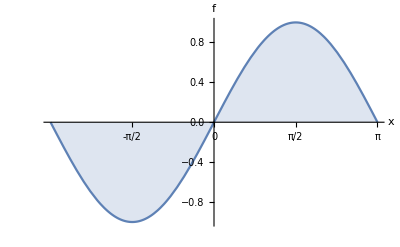

```mathematica
f[x]==Sin[x]
SCMAF[%,Plot,{At[2],{x,-π,π},Ticks->{-π/2+π/2 Range[0,4],Automatic},AxesLabel->{x,f},{Filling->Axis}},Take->{2}]
```

```mathematica
SCAFE[∫_-π^π Sin[x]ⅆx,SCEvalInt]
```

∫_-π^π Sin[x]ⅆx==0

### Indefinite Integrals

```mathematica
SCAFE[∫2xⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫2 xⅆx==C+x^2

Fundamental Theorem of Calculus - Part I

If f(x) is a continuous function on the interval [a,b] and F(x) is the indefinite integral of f(x) on [a,b], then ∫_a^b f(x)ⅆx=F(b)-F(a).

```mathematica
∫_1^3 2xⅆx==F[3]-F[1]
SCMAF[%,RA,{At[2],F[x_]==x^2+C},ApplyAll->SCEvalInt]
```

∫_1^3 2 xⅆx==-F[1]+F[3]

True

## Lab 22: Basic Integration Techniques

The antiderivative is a linear operator.

```mathematica
SCAFE[∫k f[x]ⅆx,SCFactorInt,{All,k}]
```

∫k f[x]ⅆx==k ∫f[x]ⅆx

```mathematica
SCAFE[∫(f[x]+g[x])ⅆx,SCExpandInt,All]
```

∫(f[x]+g[x])ⅆx==∫f[x]ⅆx+∫g[x]ⅆx

### Indefinite Integral of Polynomial Functions

```mathematica
SCAFE[∫x^n ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫x^n ⅆx==C+x^(1+n)/(1+n)

```mathematica
SCAFE[∫4xⅆx,SCFactorInt,Apply->SCEvalInt]
```

∫4 xⅆx==2 x^2

```mathematica
SCAFE[∫(4x-16 x^3)ⅆx,SCExpandInt,Apply->SCEvalInt]
```

∫(4 x-16 x^3)ⅆx==2 x^2-4 x^4

```mathematica
SCAFE[∫_0^(1/2) (4x-16 x^3)ⅆx,SCExpandInt,Apply->SCEvalInt]
```

∫_0^(1/2) (4 x-16 x^3)ⅆx==1/4

### Indefinite Integral of Non-Polynomial Functions

```mathematica
SCAFE[∫Cos[x]ⅆx,SCEvalInt]
```

∫Cos[x]ⅆx==Sin[x]

```mathematica
SCAFE[∫Sin[x]ⅆx,SCEvalInt]
```

∫Sin[x]ⅆx==-Cos[x]

```mathematica
SCAFE[∫Sec[x]^2 ⅆx,SCEvalInt]
```

∫Sec[x]^2 ⅆx==Tan[x]

```mathematica
SCAFE[∫Sec[x]Tan[x]ⅆx,SCEvalInt]
```

∫Sec[x] Tan[x]ⅆx==Sec[x]

```mathematica
SCAFE[∫ⅇ^x ⅆx,SCEvalInt]
```

∫ⅇ^x ⅆx==ⅇ^x

## Lab 23: Fundamental Theorem of Calculus - Part II

Based on FTC,

```mathematica
∫_a_^b_ f_ⅆx:>Subscript[Integrate[f,x], x==b]-Subscript[Integrate[f,x], x==a]
```

∫_a_^b_ f_ⅆx:>(∫fⅆx)_(x==b)-(∫fⅆx)_(x==a)

```mathematica
SCARA[{∫_0^1 x^3 ⅆx,∫_1^2 x^3 ⅆx,∫_0^2 x^3 ⅆx},∫_a_^b_ f_ⅆx_:>Subscript[Integrate[f,x], x==b]-Subscript[Integrate[f,x], x==a]]
SCMAF[%,Thread,All,Apply->SCEvalEqSub]
```

{∫_0^1 x^3 ⅆx,∫_1^2 x^3 ⅆx,∫_0^2 x^3 ⅆx}=={-(x^4/4)_(x==0)+(x^4/4)_(x==1),-(x^4/4)_(x==1)+(x^4/4)_(x==2),-(x^4/4)_(x==0)+(x^4/4)_(x==2)}

{∫_0^1 x^3 ⅆx==1/4,∫_1^2 x^3 ⅆx==15/4,∫_0^2 x^3 ⅆx==4}

```mathematica
SCARA[∫_a^b f[x]ⅆx+∫_b^c f[x]ⅆx,∫_a_^b_ f_ⅆx:>Subscript[Integrate[f,x], x==b]-Subscript[Integrate[f,x], x==a]]
SCMAF[%,RA,{All,Subscript[Integrate[f_,x_], x_==b_]-Subscript[Integrate[f_,x_], x_==a_]:>∫_a^b fⅆx}]
```

∫_a^b f[x]ⅆx+∫_b^c f[x]ⅆx==-(∫f[x]ⅆx)_(x==a)+(∫f[x]ⅆx)_(x==c)

∫_a^b f[x]ⅆx+∫_b^c f[x]ⅆx==∫_a^c f[x]ⅆx

### FTC - Part II

FTC - Part II states that if f(x) is a continuous function on [a,b], then ⅆ/ⅆx(∫_a^x f(t)ⅆt)=f(x) where x∈[a,b].

Exercises:

```mathematica
SCARA[ⅆg[x]/ⅆx,g[x]==∫_0^x Cos[t]ⅆt]
SCMAF[%,SCEvalInt,At[2],Apply->SCEvalDeriv]
```

ⅆg[x]/ⅆx==ⅆ/ⅆx∫_0^x Cos[t]ⅆt

ⅆg[x]/ⅆx==Cos[x]

```mathematica
SCARA[ⅆg[x]/ⅆx,g[x]==∫_0^(x^2) Cos[t]ⅆt]
SCMAF[%,SCEvalInt,At[2],Apply->SCEvalDeriv]
```

ⅆg[x]/ⅆx==ⅆ/ⅆx∫_0^(x^2) Cos[t]ⅆt

ⅆg[x]/ⅆx==2 x Cos[x^2]

```mathematica
SCARA[ⅆg[x]/ⅆx,g[x]==∫_0^Sin[x] Cos[t]ⅆt]
SCMAF[%,SCEvalInt,At[2],Apply->SCEvalDeriv]
```

ⅆg[x]/ⅆx==ⅆ/ⅆx∫_0^Sin[x] Cos[t]ⅆt

ⅆg[x]/ⅆx==Cos[x] Cos[Sin[x]]

```mathematica
SCARA[ⅆg[x]/ⅆx,g[x]==∫_(x^2)^(x^3) Cos[t]ⅆt]
SCMAF[%,SCEvalInt,At[2],Apply->SCEvalDeriv]
```

ⅆg[x]/ⅆx==ⅆ/ⅆx∫_(x^2)^(x^3) Cos[t]ⅆt

ⅆg[x]/ⅆx==-2 x Cos[x^2]+3 x^2 Cos[x^3]

Using only build-in functions.

```mathematica
D[Integrate[Cos[2t]/(√(t+1)),{t,1,x}],x]//Refine[#,x≥1]&//Simplify
```

Cos[2 x]/(√(1+x))

Using SymbolicComuting,

```mathematica
SCAFE[ⅆ/ⅆx∫_1^x Cos[2t]/(√(t+1))ⅆt,SCEvalInt]
SCMAF[%,Refine,{At[2],x≥1},
SCEvalDeriv,At[2],Apply->Simplify]
```

ⅆ/ⅆx∫_1^x Cos[2 t]/(√(1+t))ⅆt==ⅆ/ⅆx ConditionalExpression[√π (-Cos[2] FresnelC[2 √(2/π)]+Cos[2] FresnelC[(2 √(1+x))/(√π)]-FresnelS[2 √(2/π)] Sin[2]+Sin[2] FresnelS[(2 √(1+x))/(√π)]),Re[x]>-1||x∉ℝ]

ⅆ/ⅆx∫_1^x Cos[2 t]/(√(1+t))ⅆt==√π ⅆ/ⅆx(-Cos[2] FresnelC[2 √(2/π)]+Cos[2] FresnelC[(2 √(1+x))/(√π)]-FresnelS[2 √(2/π)] Sin[2]+Sin[2] FresnelS[(2 √(1+x))/(√π)])

ⅆ/ⅆx∫_1^x Cos[2 t]/(√(1+t))ⅆt==Cos[2 x]/(√(1+x))

## Lab 24: Substitution and Parts

### Substitution with Indefinite Integrals

```mathematica
SCAFE[∫Sin[2x]ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫Sin[2 x]ⅆx==C-1/2 Cos[2 x]

```mathematica
SCAFE[∫Sin[2x]ⅆx,SCTransInt,{All,TransVar->{x,u,2x==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],u==2x}]
```

∫Sin[2 x]ⅆx==1/2 ∫Sin[u]ⅆu

∫Sin[2 x]ⅆx==1/2 (C-Cos[u])

∫Sin[2 x]ⅆx==1/2 (C-Cos[2 x])

```mathematica
SCAFE[∫3 x^2 √(4 x^3+6)ⅆx,SCTransInt,{All,TransVar->{x,u,4 x^3+6==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->4C},
RA,{At[2],u==4 x^3+6},ExpandAll,At[2],Apply->Simplify]
```

∫3 x^2 √(6+4 x^3)ⅆx==1/4 ∫√u ⅆu

3 ∫x^2 √(6+4 x^3)ⅆx==1/4 (4 C+2/3 (6+4 x^3)^(3/2))

3 ∫x^2 √(6+4 x^3)ⅆx==C+1/3 √2 (3+2 x^3)^(3/2)

Exercises:

a.

```mathematica
SCAFE[∫(4x)/(√(x^2+6))ⅆx,SCTransInt,{All,TransVar->{x,u,6+x^2==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C/2},
RA,{At[2],u==6+x^2},Apply->Simplify]
```

∫(4 x)/(√(6+x^2))ⅆx==2 ∫1/(√u)ⅆu

4 ∫x/(√(6+x^2))ⅆx==2 (C/2+2 √u)

4 ∫x/(√(6+x^2))ⅆx==C+4 √(6+x^2)

b.

```mathematica
SCAFE[∫Sin[x]Cos[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Sin[x]==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],u==Sin[x]}]
```

∫Cos[x] Sin[x]ⅆx==∫uⅆu

∫Cos[x] Sin[x]ⅆx==C+u^2/2

∫Cos[x] Sin[x]ⅆx==C+Sin[x]^2/2

c.

```mathematica
SCAFE[∫Sin[x]Cos[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Cos[x]==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->-C},
RA,{At[2],u==Cos[x]}]
```

∫Cos[x] Sin[x]ⅆx==-∫uⅆu

∫Cos[x] Sin[x]ⅆx==C-u^2/2

∫Cos[x] Sin[x]ⅆx==C-Cos[x]^2/2

d.

This result looks different from the above result.

```mathematica
∫Cos[x] Sin[x]ⅆx==C-Cos[x]^2/2
SCMAF[%,SCEliminate,{At[2],Cos[x]^2+Sin[x]^2==1,Cos[x]^2},Apply->Expand,
RA,{At[2],-1/2+C->C}]
```

∫Cos[x] Sin[x]ⅆx==C-Cos[x]^2/2

∫Cos[x] Sin[x]ⅆx==-1/2+C+Sin[x]^2/2

∫Cos[x] Sin[x]ⅆx==C+Sin[x]^2/2

e.

```mathematica
SCAFE[∫Sec[x]Tan[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Sec[x]==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],u==Sec[x]}]
```

∫Sec[x] Tan[x]ⅆx==∫1ⅆu

∫Sec[x] Tan[x]ⅆx==C+u

∫Sec[x] Tan[x]ⅆx==C+Sec[x]

### Substitution with Definite Integrals

```mathematica
SCAFE[∫_-1^1 3 x^2 √(4 x^3+6)ⅆx,SCTransInt,{All,TransVar->{x,u,4 x^3+6==u}},Apply->SCEvalInt]
```

∫_-1^1 3 x^2 √(6+4 x^3)ⅆx==1/3 √2 (-1+5 √5)

```mathematica
SCAFE[∫_0^π Sin[x]Cos[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Cos[x]==u}},Apply->SCEvalInt]
```

∫_0^π Cos[x] Sin[x]ⅆx==0

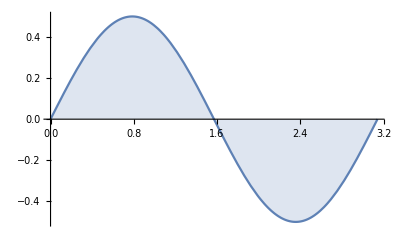

```mathematica
Plot[Sin[x]Cos[x],{x,0,π},Filling->Axis]
```

```mathematica
SCAFE[∫_0^π x Cos[x^2]ⅆx,SCTransInt,{All,TransVar->{x,u,Cos[x^2]==u}},Apply->SCEvalInt]
```

∫_0^π x Cos[x^2]ⅆx==-1/2 Sin[π^2]

### Integration by Parts

```mathematica
SCAFE[∫u[x]v'[x]ⅆx,SCIntByParts,{All,v'[x]}]
```

∫u[x] v'[x]ⅆx==-∫v[x] u'[x]ⅆx+u[x] v[x]

Exercises II:

a.

```mathematica
SCAFE[∫x ⅇ^x ⅆx,SCIntByParts,{All,ⅇ^x}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->-C}]
```

∫ⅇ^x xⅆx==ⅇ^x x-∫ⅇ^x ⅆx

∫ⅇ^x xⅆx==C-ⅇ^x+ⅇ^x x

b.

```mathematica
SCAFE[∫x Sin[x]ⅆx,SCIntByParts,{All,Sin[x]}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C}]
```

∫x Sin[x]ⅆx==-x Cos[x]+∫Cos[x]ⅆx

∫x Sin[x]ⅆx==C-x Cos[x]+Sin[x]

c.

```mathematica
SCAFE[∫x Cos[x]ⅆx,SCIntByParts,{All,Cos[x]}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->-C}]
```

∫x Cos[x]ⅆx==-∫Sin[x]ⅆx+x Sin[x]

∫x Cos[x]ⅆx==C+Cos[x]+x Sin[x]

d.

```mathematica
SCAFE[∫x^2 ⅇ^x ⅆx,SCIntByParts,{All,ⅇ^x}]
SCMAF[%,SCIntByParts,{At[2],ⅇ^x},Apply->Expand,
SCEvalInt,{At[2],ReplConst->C/2},Apply->Simplify]
```

∫ⅇ^x x^2ⅆx==ⅇ^x x^2-2 ∫ⅇ^x xⅆx

∫ⅇ^x x^2ⅆx==-2 ⅇ^x x+ⅇ^x x^2+2 ∫ⅇ^x ⅆx

∫ⅇ^x x^2ⅆx==C+ⅇ^x (2-2 x+x^2)

e.

```mathematica
SCAFE[ⅆ/ⅆx∫u[x]v'[x]ⅆx,SCIntByParts,{All,v'[x]},Apply->SCDerivExpand]
SCMAF[%,SCExpandInt,At[2],
SCIntByPartsDeriv,{∫v[x] (ⅆ^2 u[x])/(ⅆ x^2)ⅆx},
SCRestoreDeriv,At[2]]
```

ⅆ/ⅆx∫u[x] v'[x]ⅆx==-∫(ⅆu[x]/ⅆx ⅆv[x]/ⅆx+v[x] (ⅆ^2 u[x])/(ⅆ x^2))ⅆx+u[x] ⅆv[x]/ⅆx+v[x] ⅆu[x]/ⅆx

ⅆ/ⅆx∫u[x] v'[x]ⅆx==u[x] ⅆv[x]/ⅆx

ⅆ/ⅆx∫u[x] v'[x]ⅆx==u[x] v'[x]

## Lab 25: Introduction to Logarithmic Functions

### Introduction

```mathematica
SCAFE[∫Log[x]ⅆx,SCTransInt,{All,TransVar->{x,u,Log[x]==u}}]
SCMAF[%,Refine,{At[2],u∈Reals},
SCIntByParts,{At[2],ⅇ^u},
SCEvalInt,{At[2],ReplConst->-C},Apply->ExpandAll,
RA,{At[2],u==Log[x]}]
```

∫Log[x]ⅆx==∫ConditionalExpression[ⅇ^u Log[ⅇ^u],-π<Im[u]≤π]ⅆu

∫Log[x]ⅆx==C-ⅇ^u+ⅇ^u u

∫Log[x]ⅆx==C-x+x Log[x]

For general n, (n≠-1)

```mathematica
SCAFE[∫x^n ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫x^n ⅆx==C+x^(1+n)/(1+n)

```mathematica
SCAFE[∫x^-1 ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫1/x ⅆx==C+Log[x]

Exercises:

```mathematica
ⅆP/ⅆt==r P
SCMAF[%,SCDerivToFrac,At[1],
SCMultEq,{All,ⅆt/P},Apply->SCDiffToInt,
SCEvalInt,{All,ReplConst->C},
SCSubtFromEq,{All,C},
RA,{At[2],-C+C[2]->C}]
```

ⅆP/ⅆt==P r

Log[P]==-C+r t+C[2]

Log[P]==C+r t

```mathematica
Log[P]==C+r t
SCMAF[%,SCSolve,{All,P,Reals}]
```

Log[P]==C+r t

P==ⅇ^(C+r t)

```mathematica
P==ⅇ^(C+r t)
SCMAF[%,RA,{All,{P==Subscript[P, 0],t==0}},
SCSolve,{All,C,Reals},
Refine,{All,Subscript[P, 0]>0}]
```

P==ⅇ^(C+r t)

ConditionalExpression[C==Log[P_0],P_0>0]

C==Log[P_0]

```mathematica
P==ⅇ^(C+r t)/.C->Log[Subscript[P, 0]]
```

P==ⅇ^(r t) P_0

The functions ⅇ^x and ln(x) are inverse functions.

```mathematica
SCAFE[HoldForm@(ⅇ^Log[x]),ReleaseHold]
```

ⅇ^Log[x]==x

```mathematica
SCAFE[Log[ⅇ^x],FullSimplify,{All,x∈Reals}]
```

Log[ⅇ^x]==x

Some additional properties of these functions are

```mathematica
SCAFE[HoldForm@(ⅇ^x)ⅇ^y,ReleaseHold]
```

ⅇ^y ⅇ^x==ⅇ^(x+y)

```mathematica
SCAFE[HoldForm@(ⅇ^x/ⅇ^y),ReleaseHold]
```

ⅇ^x/ⅇ^y==ⅇ^(x-y)

```mathematica
SCAFE[Log[x y],PowerExpand]
```

Log[x y]==Log[x]+Log[y]

```mathematica
{Log[x y],Log[x]+Log[y]}/.{x->-1,y->-1}
```

{0,2 ⅈ π}

```mathematica
SCAFE[Log[x/y],PowerExpand]
```

Log[x/y]==Log[x]-Log[y]

```mathematica
SCAFE[Log[x^p],PowerExpand]
```

Log[x^p]==p Log[x]

```mathematica
{Log[x^p],p Log[x]}/.{x->-1,p->-1}
```

{ⅈ π,-ⅈ π}

### Derivatives and Antiderivatives Involving Logarithms

Exercises:

a.

```mathematica
SCAFE[ⅆ/ⅆx Log[x],SCEvalDeriv]
```

ⅆLog[x]/ⅆx==1/x

```mathematica
SCAFE[ⅆ/ⅆx Log[x],SCEliminate,{All,Log[x]+C==∫1/x ⅆx,Log[x]}]
SCMAF[%,SCExpandDeriv,{At[2]},(*not SCDerivExpand*)
RA,{At[2],ⅆ/ⅆx∫1/x ⅆx->1/x},Apply->SCEvalDeriv(*by FTC-II*)]
```

ⅆLog[x]/ⅆx==ⅆ/ⅆx(-C+∫1/x ⅆx)

ⅆLog[x]/ⅆx==-ⅆC/ⅆx+ⅆ/ⅆx∫1/x ⅆx

ⅆLog[x]/ⅆx==1/x

b.

```mathematica
SCAFE[HoldForm@ⅆ/ⅆx Log[b,x],ReleaseHold,Apply->SCEvalDeriv]
```

ⅆ/ⅆx(Log[b,x])==1/(x Log[b])

c.

```mathematica
Log[b,b2x[x]]==x
SCMAF[%,ⅆ/ⅆx#&,All,Level->{1},Apply->SCEvalDeriv,
SCMultEq,{All,b2x[x]Log[b]},Apply->SCAbbrevDeriv,
RA,{All,b2x->b^x}]
```

Log[b2x[x]]/Log[b]==x

ⅆb2x/ⅆx==b2x Log[b]

(ⅆ b^x)/ⅆx==b^x Log[b]

d.

```mathematica
SCAFE[∫x Log[x^2]ⅆx,SCEvalInt,{All,ReplConst->C},Apply->Simplify]
```

∫x Log[x^2]ⅆx==C-x^2/2+1/2 x^2 Log[x^2]

Using substitution,

```mathematica
SCAFE[∫x Log[x^2]ⅆx,SCTransInt,{All,TransVar->{x,u,x^2==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->2C},
RA,{At[2],u==x^2},Apply->Simplify]
```

∫x Log[x^2]ⅆx==1/2 ∫Log[u]ⅆu

∫x Log[x^2]ⅆx==1/2 (2 C-u+u Log[u])

∫x Log[x^2]ⅆx==C-x^2/2+1/2 x^2 Log[x^2]

Using integration by parts,

```mathematica
SCAFE[∫x Log[x^2]ⅆx,SCIntByParts,{All,x}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->-C}]
```

∫x Log[x^2]ⅆx==1/2 x^2 Log[x^2]-∫xⅆx

∫x Log[x^2]ⅆx==C-x^2/2+1/2 x^2 Log[x^2]

## Lab 26: Inverse Trigonometric Functions and Trigonometric Substitution

### The Inverse to cos(x)

Exercises:

a.

```mathematica
{ArcCos[1],ArcCos[-1]}
```

{0,π}

b.

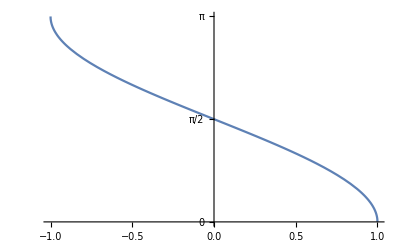

```mathematica
Plot[ArcCos[x],{x,-1,1},Ticks->{Automatic,{0,π/2,π}}]
```

c.

```mathematica
Cos[arccos[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,arccos'[x]},
RA,{At[2],arccos->ArcCos},ApplyAll->SCAbbrevDeriv]
```

Cos[arccos[x]]==x

arccos'[x]==-Csc[arccos[x]]

ⅆarccos/ⅆx==-1/(√(1-x^2))

```mathematica
SCAFE[ⅆArcCos[x]/ⅆx,SCEvalDeriv]
```

ⅆArcCos[x]/ⅆx==-1/(√(1-x^2))

### The Inverse to sin(x) and tan(x)

Exercises:

d.

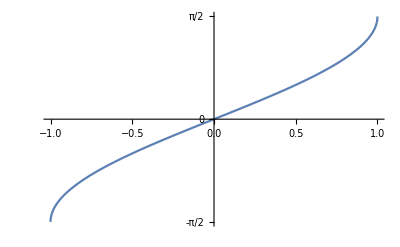

```mathematica
Plot[ArcSin[x],{x,-1,1},Ticks->{Automatic,{-π/2,0,π/2}}]
```

e.

```mathematica
Sin[arcsin[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,arcsin'[x]},
RA,{At[2],arcsin->ArcSin},ApplyAll->SCAbbrevDeriv]
```

Sin[arcsin[x]]==x

arcsin'[x]==Sec[arcsin[x]]

ⅆarcsin/ⅆx==1/(√(1-x^2))

```mathematica
SCAFE[ⅆArcSin[x]/ⅆx,SCEvalDeriv]
```

ⅆArcSin[x]/ⅆx==1/(√(1-x^2))

f.

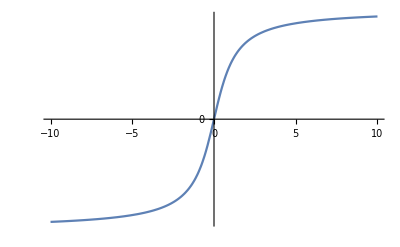

```mathematica
Plot[ArcTan[x],{x,-10,10},Ticks->{Automatic,{-π/2,0,π/2}}]
```

```mathematica
SCAFE[Underscript[Limit, x->∞][ArcTan[x]],SCEvalLimit]
```

Limit_(x→∞)[ArcTan[x]]==π/2

```mathematica
Tan[arctan[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,arctan'[x]},
RA,{At[2],arctan->ArcTan},Apply->SCAbbrevDeriv]
```

Tan[arctan[x]]==x

arctan'[x]==Cos[arctan[x]]^2

arctan'[x]==1/(1+x^2)

```mathematica
SCAFE[ⅆArcTan[x]/ⅆx,SCEvalDeriv]
```

ⅆArcTan[x]/ⅆx==1/(1+x^2)

### Applying Your Knowledge

ⅆArcCot[x]/ⅆx

```mathematica
Cot[arccot[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,,
SCSolve,{All,arccot'[x]},
RA,{At[2],arccot->ArcCot},Apply->ExpandAll,ApplyAll->SCAbbrevDeriv]
```

Cot[arccot[x]]==x

-Csc[arccot[x]]^2 arccot'[x]==1

arccot'[x]==-Sin[arccot[x]]^2

ⅆarccot/ⅆx==-1/(1+x^2)

```mathematica
SCAFE[ⅆArcCot[x]/ⅆx,SCEvalDeriv]
```

ⅆArcCot[x]/ⅆx==-1/(1+x^2)

ⅆArcSec[x]/ⅆx

```mathematica
Sec[arcsec[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,arcsec'[x]},
RA,{At[2],arcsec->ArcSec},ApplyAll->SCAbbrevDeriv]
```

Sec[arcsec[x]]==x

arcsec'[x]==Cos[arcsec[x]] Cot[arcsec[x]]

ⅆarcsec/ⅆx==1/(x^2 √(1-1/x^2))

```mathematica
SCAFE[ⅆArcSec[x]/ⅆx,SCEvalDeriv]
```

ⅆArcSec[x]/ⅆx==1/(x^2 √(1-1/x^2))

ⅆArcCsc[x]/ⅆx

```mathematica
Csc[arccsc[x]]==x
SCMAF[%,(ⅆ#)/ⅆx&,All,Level->{1},Apply->SCEvalDeriv,
SCSolve,{All,arccsc'[x]},
RA,{At[2],arccsc->ArcCsc},ApplyAll->SCAbbrevDeriv]
```

Csc[arccsc[x]]==x

arccsc'[x]==-Sin[arccsc[x]] Tan[arccsc[x]]

ⅆarccsc/ⅆx==-1/(x^2 √(1-1/x^2))

```mathematica
SCAFE[ⅆArcCsc[x]/ⅆx,SCEvalDeriv]
```

ⅆArcCsc[x]/ⅆx==-1/(x^2 √(1-1/x^2))

Exercises:

h.

```mathematica
SCARA[ⅆ/ⅆx ArcTan[ⅇ^(2x)],ⅆArcTan[f_]/ⅆx:> 1/(1+f^2)ⅆf/ⅆx,Apply->SCEvalDeriv]
```

ⅆArcTan[ⅇ^(2 x)]/ⅆx==(2 ⅇ^(2 x))/(1+ⅇ^(4 x))

```mathematica
SCAFE[ⅆ/ⅆx ArcTan[ⅇ^(2x)],SCEvalDeriv]
```

ⅆArcTan[ⅇ^(2 x)]/ⅆx==(2 ⅇ^(2 x))/(1+ⅇ^(4 x))

i.

```mathematica
SCAFE[∫1/(1+x^2)ⅆx,SCTransInt,{All,TransVar->{x,u,x==Tan[u]}},Apply->Simplify]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},
SCEliminate,{At[2],x==Tan[u],u},
Refine,{All,C[1]==0}]
```

∫1/(1+x^2)ⅆx==∫1ⅆu

ConditionalExpression[∫1/(1+x^2)ⅆx==C+ArcTan[x]+π C[1],C[1]∈ℤ]

∫1/(1+x^2)ⅆx==C+ArcTan[x]

```mathematica
SCAFE[∫1/(1+x^2)ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫1/(1+x^2)ⅆx==C+ArcTan[x]

j.

```mathematica
SCAFE[∫1/(√(1-16 x^2))ⅆx,SCTransInt,{All,TransVar->{x,u,4x==u}}]
SCMAF[%,RA,{At[2],∫1/(√(1-u^2))ⅆu==ArcSin[u]+4C},Apply->ExpandAll,
SCEliminate,{At[2],4x==u,u}]
```

∫1/(√(1-16 x^2))ⅆx==1/4 ∫1/(√(1-u^2))ⅆu

∫1/(√(1-16 x^2))ⅆx==C+ArcSin[u]/4

∫1/(√(1-16 x^2))ⅆx==C+1/4 ArcSin[4 x]

```mathematica
SCAFE[∫1/(√(1-16 x^2))ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫1/(√(1-16 x^2))ⅆx==C+1/4 ArcSin[4 x]

k.

```mathematica
SCAFE[∫x/(x^2+9)ⅆx,SCTransInt,{All,TransVar->{x,u,x/3==u}}]
SCMAF[%,Factor,{9+9 u^2},
RA,{At[2],∫u/(1+u^2)ⅆu==1/2 Log[1+u^2]+c},
SCEliminate,{At[2],x/3==u,u},Apply->Simplify,
FunctionExpand,At[2],Apply->Expand,
RA,{At[2],c-Log[9]/2->c}]
```

∫x/(9+x^2)ⅆx==9 ∫u/(9+9 u^2)ⅆu

∫x/(9+x^2)ⅆx==c-Log[9]/2+1/2 Log[9+x^2]

∫x/(9+x^2)ⅆx==c+1/2 Log[9+x^2]

```mathematica
SCAFE[∫x/(x^2+9)ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫x/(9+x^2)ⅆx==C+1/2 Log[9+x^2]

#### Trigonometric Substitution

Exercises:

a.

```mathematica
SCAFE[∫√(4-x^2)ⅆx,SCTransInt,{All,TransVar->{x,θ,x==2Sin[θ]}},Apply->Simplify]
SCMAF[%,Simplify,{At[2],-π/2≤θ≤π/2},
SCEvalInt,{At[2],ReplConst->C},Apply->Simplify,
SCEliminate,{At[2],x==2Sin[θ],θ}]
```

∫√(4-x^2)ⅆx==4 ∫Cos[θ] √(Cos[θ]^2)ⅆθ

∫√(4-x^2)ⅆx==4 C+2 θ+Sin[2 θ]

∫√(4-x^2)ⅆx=={{ConditionalExpression[4 C+2 (π-ArcSin[x/2]+2 π C[1])+Sin[2 (π-ArcSin[x/2]+2 π C[1])],C[1]∈ℤ]},{ConditionalExpression[4 C+2 (ArcSin[x/2]+2 π C[1])+Sin[2 (ArcSin[x/2]+2 π C[1])],C[1]∈ℤ]}}

Why does the result so complicated?

```mathematica
Solve[x==2Sin[θ],θ]
```

{{θ→ConditionalExpression[π-ArcSin[x/2]+2 π C[1],C[1]∈ℤ]},{θ→ConditionalExpression[ArcSin[x/2]+2 π C[1],C[1]∈ℤ]}}

Then, which one is an adequate solution?

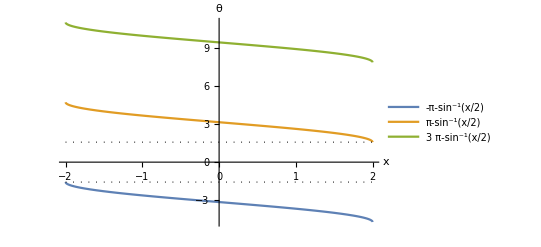

```mathematica
Plot[Evaluate@Table[π-ArcSin[x/2]+2 π C,{C,-1,1}],{x,-2,2},PlotLegends->"Expressions",AxesLabel->{x,θ},Epilog->{Dotted,Line[{{-2,π/2},{2,π/2}}],Line[{{-2,-π/2},{2,-π/2}}]}]
```

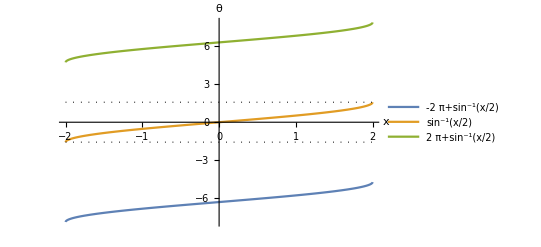

```mathematica
Plot[Evaluate@Table[ArcSin[x/2]+2 π C,{C,-1,1}],{x,-2,2},PlotLegends->"Expressions",AxesLabel->{x,θ},Epilog->{Dotted,Line[{{-2,π/2},{2,π/2}}],Line[{{-2,-π/2},{2,-π/2}}]}]
```

```mathematica
∫√(4-x^2)ⅆx==4 C+2 θ+Sin[2 θ]
SCMAF[%,RA,{At[2],θ==ArcSin[x/2]},Apply->TrigExpand,
SCFactor,{1-x^2/4,1/4},
RA,{At[2],4 C->C}]
```

∫√(4-x^2)ⅆx==4 C+2 θ+Sin[2 θ]

∫√(4-x^2)ⅆx==4 C+1/2 x √(4-x^2)+2 ArcSin[x/2]

∫√(4-x^2)ⅆx==C+1/2 x √(4-x^2)+2 ArcSin[x/2]

```mathematica
Integrate[√(4-x^2),x]
```

1/2 x √(4-x^2)+2 ArcSin[x/2]

d.

```mathematica
SCAFE[∫1/(√(4-x^2))ⅆx,SCTransInt,{All,TransVar->{x,θ,x==2Cos[θ]}},Apply->Simplify]
SCMAF[%,Simplify,{At[2],0≤θ≤π},
SCEvalInt,{At[2],ReplConst->-C},
SCEliminate,{All,x==2Cos[θ],θ}]
```

∫1/(√(4-x^2))ⅆx==-∫Csc[θ] √(Sin[θ]^2)ⅆθ

∫1/(√(4-x^2))ⅆx==C-θ

{{ConditionalExpression[∫1/(√(4-x^2))ⅆx==C+ArcCos[x/2]-2 π C[1],C[1]∈ℤ]},{ConditionalExpression[∫1/(√(4-x^2))ⅆx==C-ArcCos[x/2]-2 π C[1],C[1]∈ℤ]}}

Choose an adequate form of θ to fit the range 0≤θ≤π.

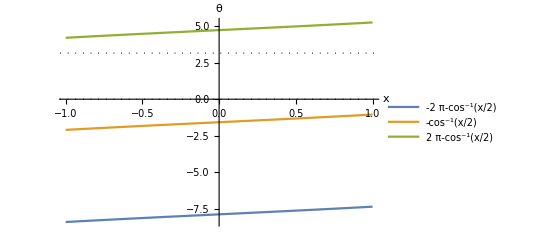

```mathematica
Plot[Evaluate@Table[-ArcCos[x/2]+2 π C,{C,-1,1}],{x,-1,1},PlotLegends->"Expressions",AxesLabel->{x,θ},Epilog->{Dotted,Line[{{-2,0},{2,0}}],Line[{{-2,π},{2,π}}]}]
```

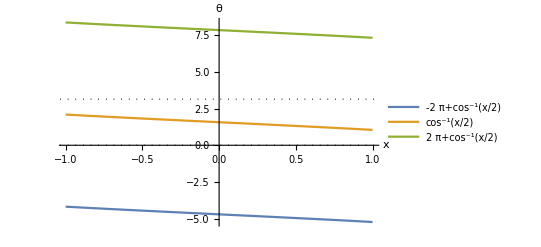

```mathematica
Plot[Evaluate@Table[ArcCos[x/2]+2 π C,{C,-1,1}],{x,-1,1},PlotLegends->"Expressions",AxesLabel->{x,θ},Epilog->{Dotted,Line[{{-2,0},{2,0}}],Line[{{-2,π},{2,π}}]}]
```

```mathematica
∫1/(√(4-x^2))ⅆx==C-θ
SCMAF[%,RA,{At[2],θ==ArcCos[x/2]}]
```

∫1/(√(4-x^2))ⅆx==C-θ

∫1/(√(4-x^2))ⅆx==C-ArcCos[x/2]

Check the result with the solution from built-in function.

```mathematica
SCAFE[∫1/(√(4-x^2))ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫1/(√(4-x^2))ⅆx==C+ArcSin[x/2]

The two solutions just differ by a constant.

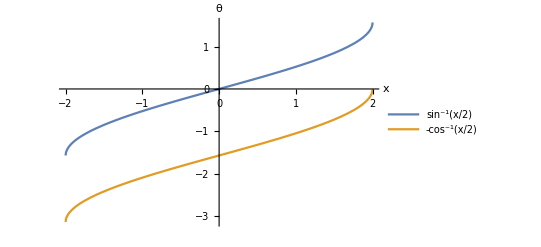

```mathematica
Plot[{ArcSin[x/2],-ArcCos[x/2]},{x,-2,2},AxesLabel->{x,θ},PlotLegends->"Expressions"]
```

```mathematica
∫1/(√(4-x^2))ⅆx==C-ArcCos[x/2]
SCMAF[%,RA,{At[2],C->C+π/2},Apply->FullSimplify]
```

∫1/(√(4-x^2))ⅆx==C-ArcCos[x/2]

∫1/(√(4-x^2))ⅆx==C+ArcSin[x/2]

e.

```mathematica
SCAFE[∫x/(√(9+x^2))ⅆx,SCTransInt,{All,TransVar->{x,u,x^2+9==u}}]
SCMAF[%,SCEvalInt,{At[2],ReplConst->2C},
RA,{At[2],Reverse[x^2+9==u]},Apply->Expand]
```

∫x/(√(9+x^2))ⅆx==1/2 ∫1/(√u)ⅆu

∫x/(√(9+x^2))ⅆx==1/2 (2 C+2 √u)

∫x/(√(9+x^2))ⅆx==C+√(9+x^2)

```mathematica
SCAFE[∫x/(√(9+x^2))ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫x/(√(9+x^2))ⅆx==C+√(9+x^2)

## Lab 27: Partial Fractions

### Introduction

```mathematica
SCAFE[∫(2x+3)/(x^2-5x+4)ⅆx,Apart,(2x+3)/(x^2-5x+4),ApplyAll->SCExpandInt]
SCMAF[%,SCTransInt,{{∫1/(-4+x)ⅆx,TransVar->{x,u,-4+x==u}},{∫1/(-1+x)ⅆx,TransVar->{x,v,-1+x==v}}},
SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],{u==x-4,v==x-1}},Apply->ExpandAll,
RA,{At[2],(11 C)/3-(5 C[2])/3->C}]
```

∫(3+2 x)/(4-5 x+x^2)ⅆx==11/3 ∫1/(-4+x)ⅆx-5/3 ∫1/(-1+x)ⅆx

∫(3+2 x)/(4-5 x+x^2)ⅆx==(11 C)/3-(5 C[2])/3+11/3 Log[-4+x]-5/3 Log[-1+x]

∫(3+2 x)/(4-5 x+x^2)ⅆx==C+11/3 Log[-4+x]-5/3 Log[-1+x]

```mathematica
SCAFE[∫(2x+3)/(x^2-5x+4)ⅆx,SCEvalInt,{All,ReplConst->C}]
```

∫(3+2 x)/(4-5 x+x^2)ⅆx==C-5/3 Log[1-x]+11/3 Log[4-x]

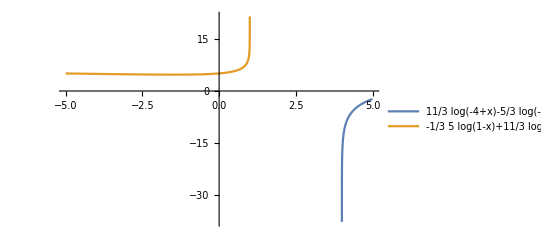

```mathematica
Plot[{11/3 Log[-4+x]-5/3 Log[-1+x],-5/3 Log[1-x]+11/3 Log[4-x]},{x,-5,5},PlotRange->All,PlotLegends->"Expressions"]
```

What is wrong? 
Answer: 
Integrate[1/x, x] should give Log[Abs[x]] but does not ?

```mathematica
SCAFE[∫(2x+3)/(x^2-5x+4)ⅆx,Apart,(2x+3)/(x^2-5x+4),ApplyAll->SCExpandInt]
SCMAF[%,SCTransInt,{{∫1/(-4+x)ⅆx,TransVar->{x,u,-4+x==u}},{∫1/(-1+x)ⅆx,TransVar->{x,v,-1+x==v}}},
SCEvalInt,{At[2],ReplConst->C},
RA,{At[2],{u==x-4,v==x-1}},Apply->ExpandAll,
RR,{At[2],{(11 C)/3-(5 C[2])/3->C,Log[x_]->Log[Abs[x]]}}]
```

∫(3+2 x)/(4-5 x+x^2)ⅆx==11/3 ∫1/(-4+x)ⅆx-5/3 ∫1/(-1+x)ⅆx

∫(3+2 x)/(4-5 x+x^2)ⅆx==(11 C)/3-(5 C[2])/3+11/3 Log[-4+x]-5/3 Log[-1+x]

∫(3+2 x)/(4-5 x+x^2)ⅆx==C+11/3 Log[|-4+x|]-5/3 Log[|-1+x|]

Exercise:

a.

```mathematica
SCAFE[∫(4x-3)/(2 x^3-3 x^2+x)ⅆx,Apart,{(4x-3)/(2 x^3-3 x^2+x)},ApplyAll->SCExpandInt]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},Apply->ExpandAll,
RR,{At[2],{Arg[x_]->0,C-3 C[2]+4 C[3]->C,Log[x_]->Log[Abs[x]]}},
Apply->Simplify]
```

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==∫1/(-1+x)ⅆx-3 ∫1/x ⅆx+4 ∫1/(-1+2 x)ⅆx

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==C-3 C[2]+4 C[3]+Log[-1+x]-3 Log[x]+2 Log[-1+2 x]

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==C+2 Log[|1-2 x|]+Log[|-1+x|]-3 Log[|x|]

```mathematica
SCAFE[∫(4x-3)/(2 x^3-3 x^2+x)ⅆx,SCEvalInt,{All,ReplConst->C}]
SCMAF[%,RA,{At[2],{Log[x_]->Log[Abs[x]]}},
Apply->Simplify]
```

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==C+2 Log[1-2 x]+Log[1-x]-3 Log[x]

∫(-3+4 x)/(x-3 x^2+2 x^3)ⅆx==C+2 Log[|1-2 x|]+Log[|1-x|]-3 Log[|x|]

b.

```mathematica
SCAFE[∫(3 x^2-1)/(x^3-4x)ⅆx,Apart,{(3 x^2-1)/(x^3-4x)},ApplyAll->SCExpandInt]
SCMAF[%,SCEvalInt,{At[2],ReplConst->C},Apply->ExpandAll,
RR,{At[2],{(11 C)/8+C[2]/4+(11 C[3])/8->C,Log[x_]->Log[Abs[x]]}},
Apply->Simplify]
```

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==11/8 ∫1/(-2+x)ⅆx+1/4 ∫1/x ⅆx+11/8 ∫1/(2+x)ⅆx

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==(11 C)/8+C[2]/4+(11 C[3])/8+11/8 Log[-2+x]+Log[x]/4+11/8 Log[2+x]

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==1/8 (8 C+11 Log[|-2+x|]+2 Log[|x|]+11 Log[|2+x|])

```mathematica
SCAFE[∫(3 x^2-1)/(x^3-4x)ⅆx,SCEvalInt,{All,ReplConst->C}]
SCMAF[%,RA,{At[2],{Log[x_]->Log[Abs[x]]}},
Apply->Simplify]
```

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==C+Log[x]/4+11/8 Log[4-x^2]

∫(-1+3 x^2)/(-4 x+x^3)ⅆx==C+1/4 Log[|x|]+11/8 Log[|4-x^2|]

Demonstration: Find the Coefficients of a Partial Fraction Decomposition

```mathematica
(4x-2)/(x^3-4 x^2+4x)==A/x+B/(x-2)+C/(x-2)^2
SCMAF[%,SCMultEq,{All,x^3-4 x^2+4x},Apply->Simplify,
{#,(∂#)/(∂x),(∂^2 #)/(∂x^2)}&,All,
Thread,{All,Equal},Level->{1},Apply->SCEvalDeriv,
RA,{All,x->0},
SCSolve,{All,{A,B,C}}]
```

(-2+4 x)/(4 x-4 x^2+x^3)==C/(-2+x)^2+B/(-2+x)+A/x

{0==2+4 A,4==-4 A-2 B+C,0==2 A+2 B}

{A==-1/2,B==1/2,C==3}

The same idea, but with different method,

```mathematica
(4x-2)/(x^3-4 x^2+4x)==A/x+B/(x-2)+C/(x-2)^2
SCMAF[%,SCMultEq,{All,x^3-4 x^2+4x},Apply->Simplify,
SCSubtFromEq,{All,4x},Apply->Reverse]
```

(-2+4 x)/(4 x-4 x^2+x^3)==C/(-2+x)^2+B/(-2+x)+A/x

4 x==2+A (-2+x)^2+C x+B (-2+x) x

2+A (-2+x)^2-4 x+C x+B (-2+x) x==0

```mathematica
CoefficientList[2+A (-2+x)^2-4 x+C x+B (-2+x) x,x]==0//Thread
SCMAF[%,SCSolve,{All,{A,B,C}}]
```

{2+4 A==0,-4-4 A-2 B+C==0,A+B==0}

{A==-1/2,B==1/2,C==3}

d.

```mathematica
(4x-2)/(x^3-4 x^2+4x)==A/x+B/(x-2)+C/(x-2)^2
SCMAF[%,RA,{All,{A==-1/2,B==1/2,C==3}},Apply->Simplify]
```

(-2+4 x)/(4 x-4 x^2+x^3)==C/(-2+x)^2+B/(-2+x)+A/x

True